```mathematica
DSolve[k'[t]==s*k[t]^a-m*k[t],k[t],t]//FullSimplify
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
mk[t_]:=InverseFunction[(0.5* Log[#1]-Log[0.2 #1-0.3 #1^(1/2)])/((-1+0.5) *0.2)&][-t+C[1]]
```

```mathematica
Plot[mk[t],{t,0,10}]
```

$Aborted

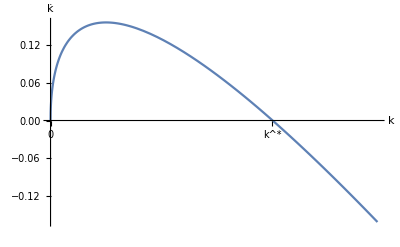

```mathematica
L=Plot[0.5*Sqrt[t]-0.4*t,{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k,k̇},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf",L,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig1.pdf

```mathematica
"D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf"
```

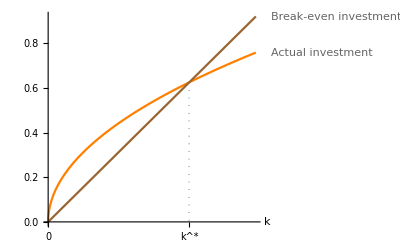

```mathematica
L2=Show[Plot[{0.5*Sqrt[t],0.4*t},{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->{"Actual investment","Break-even investment"},PlotStyle->{Orange,Brown}],ParametricPlot[{1.561,t},{t,0.006,0.615},PlotStyle->{Dotted,Thickness[Medium]}]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf",L2,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig1.pdf

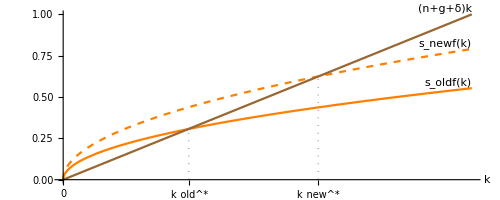

```mathematica
L3=Show[Plot[{0.5*Sqrt[t],0.35*Sqrt[t],0.4*t},{t,0,2.5},Ticks->{{{0,"0"},{0.768,"k_old^*"},{1.56,"k_new^*"}},None},AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->Placed[{Style["s_newf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["s_oldf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["(n+g+δ)k",Italic,FontSize->11,FontFamily->"Times New Roman"]},{Scaled[1],Above}],PlotStyle->{{Orange,Dashed},Orange,Brown}],ParametricPlot[{1.56,t},{t,0.002,0.622},PlotStyle->{Dotted,Thickness[Medium]}],ParametricPlot[{0.768,t},{t,0.002,0.31},PlotStyle->{Dotted,Thickness[Medium]}]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig3.pdf",L3,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig3.pdf

```mathematica
L4=-Graphics-
```

-Graphics-

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig3.pdf",L4,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig3.pdf

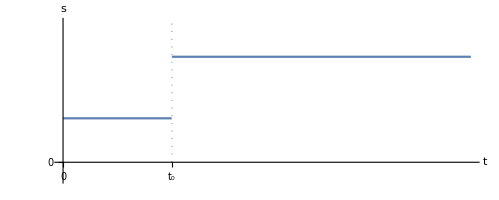

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_1.pdf

```mathematica
L5=Show[Plot[Piecewise[{{0.25,t<0.6},{0.6,0.6<t}}],{t,0,2.25},Ticks->{{{0,"0"},{0.6,"t_0"}},{{0,"0"}}},AxesLabel->{t,s},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-0.1,0.8}],ParametricPlot[{0.6,t},{t,0.002,0.8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_1.pdf",L5,ImageResolution->1500]
```

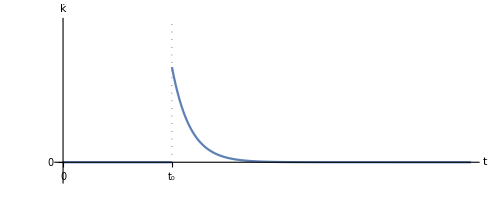

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_2.pdf

```mathematica
L6=Show[Plot[Piecewise[{{0,t<6},{2200/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,k̇},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_2.pdf",L6,ImageResolution->1500]
```

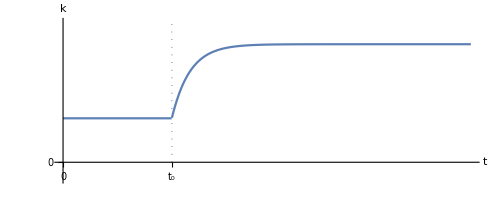

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_3.pdf

```mathematica
L7=Show[Plot[Piecewise[{{2.5,t<6},{6.71388-1700/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,k},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_3.pdf",L7,ImageResolution-> 1500]
```

```mathematica
Solve[2.5==x-1700/E^(6),x]
```

{{x→6.71388}}

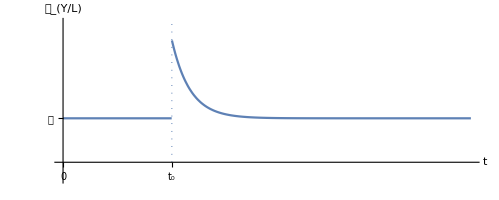

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_4.pdf

```mathematica
L8=Show[Plot[Piecewise[{{2.5,t<6},{2.5+1800/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{2.5,"ℊ"}}},AxesLabel->{t,Subscript[ℊ, Y/L]},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_4.pdf",L8,ImageResolution->1500]
```

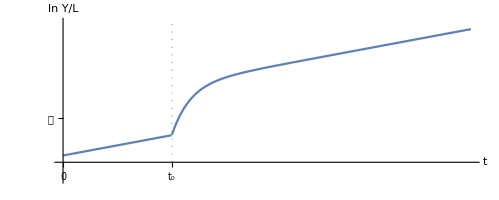

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_5.pdf

```mathematica
L9=Show[Plot[Piecewise[{{2.5*t+5,t<=6},{2.5*t-15000/E^(t)+42.18128,6<t}}]/13,{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{2.5,"ℊ"}}},AxesLabel->{t,"ln"InputForm[Y/L]},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_5.pdf",L9,ImageResolution->1500]
```

```mathematica
L10=Show[Plot[Piecewise[{{6,t<6},{6.71388-20/E^(t/4),6<t<10},{-10000,t>=10}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,c},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig6.pdf",L10,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig6.pdf

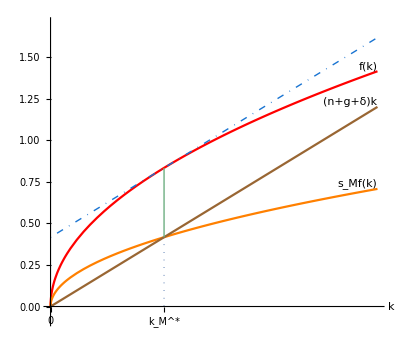

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig5_2.pdf

```mathematica
L11=Show[Plot[{Sqrt[t],0.5*Sqrt[t],0.6*t,0.6*t+5/12},{t,0,2},Ticks->{{{0,"0"},{25/36,"k_M^*"}},None},  AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->Placed[{Style["f(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["s_Mf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["(n+g+δ)k",Italic,FontSize->11,FontFamily->"Times New Roman"]},{Scaled[1],Above}],PlotRange->{-0.08,1.7},PlotStyle->{Red,Orange,Brown,{ColorData["Crayola"]["NavyBlue"],DotDashed,,Thickness[Medium]}}],ParametricPlot[{25/36,t},{t,0.002,5/12},PlotStyle->{Dotted,Thickness[Medium]}],ParametricPlot[{25/36,t},{t,5/12,5/6},PlotLabel->c,PlotStyle->{ColorData["Crayola"]["ForestGreen"],Thickness[Medium]}]]
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig5_2.pdf",L11,ImageResolution->1500]
```

```mathematica
1/4/0.36
```

0.694444

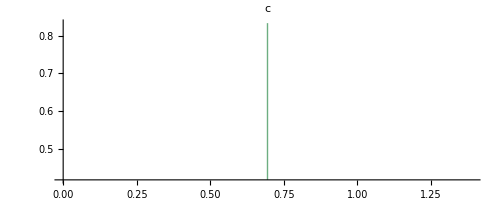

```mathematica
ParametricPlot[{25/36,t},{t,5/12,5/6},PlotLabel->c,PlotStyle->{ColorData["Crayola"]["ForestGreen"],Thickness[Medium]}]
```

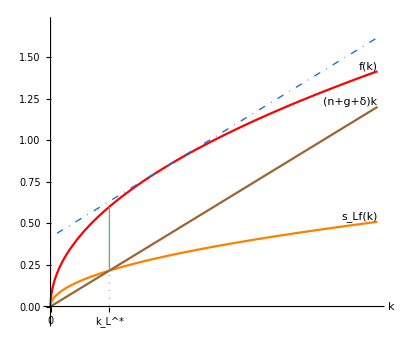

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig5_1.pdf

```mathematica
L12=Show[Plot[{Sqrt[t],0.36*Sqrt[t],0.6*t,0.6*t+5/12},{t,0,2},Ticks->{{{0,"0"},{9/25,"k_L^*"}},None},  AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->Placed[{Style["f(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["s_Lf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["(n+g+δ)k",Italic,FontSize->11,FontFamily->"Times New Roman"]},{Scaled[1],Above}],PlotRange->{-0.08,1.7},PlotStyle->{Red,Orange,Brown,{ColorData["Crayola"]["NavyBlue"],DotDashed,,Thickness[Medium]}}],ParametricPlot[{9/25,t},{t,0.002,27/125},PlotStyle->{Dotted,Thickness[Medium]}],ParametricPlot[{9/25,t},{t,27/125,3/5},PlotLabel->c,PlotStyle->{ColorData["Crayola"]["ForestGreen"],Thickness[Medium]}]]
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig5_1.pdf",L12,ImageResolution->1500]
```

```mathematica
Solve[0.64*Sqrt[t]==0.6*t,t]
0.6*1.1377777777777778
Sqrt[1.1377777777777778]
```

{{t→0.},{t→1.13778}}

0.682667

1.06667

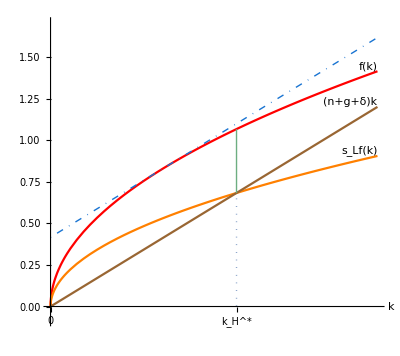

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig5_3.pdf

```mathematica
L13=Show[Plot[{Sqrt[t],0.64*Sqrt[t],0.6*t,0.6*t+5/12},{t,0,2},Ticks->{{{0,"0"},{1.137778,"k_H^*"}},None},  AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->Placed[{Style["f(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["s_Lf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["(n+g+δ)k",Italic,FontSize->11,FontFamily->"Times New Roman"]},{Scaled[1],Above}],PlotRange->{-0.08,1.7},PlotStyle->{Red,Orange,Brown,{ColorData["Crayola"]["NavyBlue"],DotDashed,,Thickness[Medium]}}],ParametricPlot[{1.137778,t},{t,0.002,0.682667},PlotStyle->{Dotted,Thickness[Medium]}],ParametricPlot[{1.137778,t},{t,0.682667,1.06667},PlotLabel->c,PlotStyle->{ColorData["Crayola"]["ForestGreen"],Thickness[Medium]}]]
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig5_3.pdf",L13,ImageResolution->1500]
```

```mathematica
NDSolve[{k'[t]==Sqrt[k[t]]-c[t]-k[t]/2,c'[t]/c[t]==(1/(2*Sqrt[k[t]])-4/5-1/4)/(1/2),k[0]==1,c[0]==1/2},{k,c},{t,0,100}]
```

{{k→InterpolatingFunction[{{0., 100.}}, <>],c→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
Plot[InterpolatingFunction[{{0., 10.}}, <>]]
```

General::noinfo: Input expression InterpolatingFunction[{{0., 10.}}, <>] contains insufficient information to interpret the result.

```mathematica
F=Show[Plot[5*t^(2/3)-3*t,{t,0,125/27},Ticks->{{{0,"0"},{1,"k^*"}},None},AxesLabel->{k,c},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-0.08,4}],ParametricPlot[{1,t},{t,0,3.8},PlotLabel->"jj",PlotStyle->{Orange,Thickness[Medium]}],ParametricPlot[{1,t},{t,2,2.0001},PlotLabel->"E",PlotStyle->{Black,Thickness[0.01]}]]
```

```mathematica
Solve[5*t^(2/3)-3*t==0,t]
```

{{t→0},{t→125/27}}

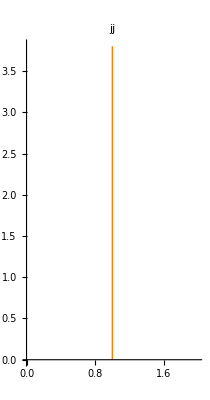

```mathematica
ParametricPlot[{1,t},{t,0,3.8},PlotLabel->"jj",PlotStyle->{Orange,Thickness[Medium]}]
```

```mathematica
F2=-Graphics-
```

-Graphics-

```mathematica
F3=-Graphics-
```

```mathematica
F3=-Graphics-
```

-Graphics-

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig7.pdf",F3,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig7.pdf

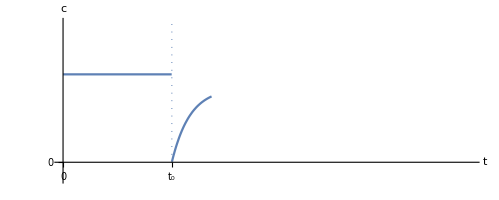

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig6.pdf

```mathematica
F6=Show[Plot[Piecewise[{{5,t<6},{1700/E^(6)-1700/E^(t),6<t<8.2},{-111,t>8.2}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,c},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig6.pdf",F6,ImageResolution-> 1500]
```